# Relative degree

## Two mass system

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{x1}, {x2}, {x3}, {x4}});
```

#### Equation of motion Mx’’ + B = Hu

```mathematica
M=({{m1, 0}, {0, m2}});
```

```mathematica
B=({{k, -k}, {-k, k}}).({{x3}, {x4}})+({{s, -s}, {-s, s}}).({{x1}, {x2}});
```

```mathematica
H=({{1}, {0}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H u-B);
```

```mathematica
xdot ={{x3}, {x4},inv[[1]],inv[[2]]}
```

{{x3},{x4},{(u-s x1+s x2-k x3+k x4)/m1},{(s x1-s x2+k x3-k x4)/m2}}

```mathematica
gx=Coefficient[xdot,u]
```

{{0},{0},{1/m1},{0}}

```mathematica
fx=xdot-gx u//Simplify
```

{{x3},{x4},{(s (-x1+x2)+k (-x3+x4))/m1},{(s x1-s x2+k x3-k x4)/m2}}

### x1 output

```mathematica
hx=x1;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{1/m1}}

#### ==> r=2

### x2 output

```mathematica
hx=x2;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x4}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{0}}

#### L_g(L^2)_fh(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx
```

{{(s x1-s x2+k x3-k x4)/m2}}

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx
```

{{{k/(m1 m2)}}}

#### ==> r=3

## Cart pole system

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{x1}, {x2}, {x3}, {x4}});
```

#### Equation of motion Mx’’ + B = Hu

```mathematica
M=({{m1+m2, m2 l Cos[x2]}, {m2 l Cos[x2], m2 l^2}});
```

```mathematica
B=({{0}, {-m2 l x4^2 Sin[x2]+m2 g l Sin[x2]}});
```

```mathematica
H=({{1}, {0}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H u-B);
```

```mathematica
xdot ={{x3}, {x4},inv[[1]],inv[[2]]};
```

```mathematica
gx=Coefficient[xdot,u]
```

{{0},{0},{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)},{-(l m2 Cos[x2])/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
fx=xdot-gx u//Simplify
```

{{x3},{x4},{-(m2 (-g+x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)},{-((m1+m2) (g-x4^2) Sin[x2])/(l (m1+m2-m2 Cos[x2]^2))}}

### Cart position output

```mathematica
hx=x1;
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
LgLfhx/.x2->0
```

{{1/m1}}

#### ==> r=2

### Pole x coordinate output

```mathematica
hx=x1+l Sin[x2];
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{x3+l x4 Cos[x2]}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx
```

{{(l^2 m2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)-(l^2 m2 Cos[x2]^2)/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}

```mathematica
LgLfhx/.x2->0
```

{{0}}

#### ==> r=2 if φ ≠ 0 + kπ

#### L_g(L^2)_fh(x) k=2

```mathematica
Lf2hx=D[Lfhx,Transpose[x]].fx
```

{{-l x4^2 Sin[x2]-((m1+m2) (g-x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)-(m2 (-g+x4^2) Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)}}

```mathematica
LgLf2hx=D[Lf2hx,Transpose[x]].gx
```

{{{-(l m2 Cos[x2] (-2 l x4 Sin[x2]-(2 m2 x4 Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)+(2 (m1+m2) x4 Cos[x2] Sin[x2])/(m1+m2-m2 Cos[x2]^2)))/(l^2 m1 m2+l^2 m2^2-l^2 m2^2 Cos[x2]^2)}}}

```mathematica
LgLf2hx/.x2->0
```

{{{0}}}

#### L_g(L^3)_fh(x) k=3

```mathematica
Lf3hx=D[Lf2hx,Transpose[x]].fx;
```

```mathematica
LgLf3hx=D[Lf3hx,Transpose[x]].gx;
```

```mathematica
LgLf3hx/.x2->0//FullSimplify
```

{{{{(g+3 (-1+l) x4^2)/(l m1)}}}}

```mathematica
Solve[(g+3 (-1+l) x4^2)/(l m1)==0,x4]
```

{{x4→-(√g)/(√3 √(1-l))},{x4→(√g)/(√3 √(1-l))}}

#### ==> r=4 if φ = 0 + kπ and φ’ ≠ ± (√g)/(√3 √(1-l))

#### L_g(L^4)_fh(x) k=4

```mathematica
Lf4hx=D[Lf3hx,Transpose[x]].fx;
```

```mathematica
LgLf4hx=D[Lf4hx,Transpose[x]].gx;
```

```mathematica
LgLf4hx/.x2->0//FullSimplify
```

{{{{{0}}}}}

#### ==> r=5 if φ = 0 + kπ and φ’ = ± (√g)/(√3 √(1-l))

## Space robot

```mathematica
ClearAll["Global`*"]
```

```mathematica
x=({{q0[t]}, {q1[t]}, {q2[t]}, {q0'[t]}, {q1'[t]}, {q2'[t]}});
```

#### Equation of motion Mx’’ + C = Hu

### Elements of Mass Matrix

```mathematica
m11=1/(4 (m0+m1+m2))(4 I0 m0+4 I1 m0+4 I2 m0+4 I0 m1+4 I1 m1+4 I2 m1+4 l0^2 m0 m1+l1^2 m0 m1+4 I0 m2+4 I1 m2+4 I2 m2+4 l0^2 m0 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+4 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m12=1/(4 (m0+m1+m2))(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m13=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m21=1/(4 (m0+m1+m2))(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]);
```

```mathematica
m22=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+l1^2 m0 m1+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 I1 (m0+m1+m2)+2 l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m23=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])/(4 (m0+m1+m2));
```

```mathematica
m31=1/(4 (m0+m1+m2))(4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]]);
```

```mathematica
m32=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])/(4 (m0+m1+m2));
```

```mathematica
m33=(l2^2 (m0+m1) m2+4 I2 (m0+m1+m2))/(4 (m0+m1+m2));
```

### Elements of C Matrix

```mathematica
c1=1/(4 (m0+m1+m2))(2 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q1'[t]^2-2 l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q1'[t] q2'[t]-l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q2'[t]^2+q0'[t] (4 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q1'[t]-2 l2 m2 (-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q2'[t]));
```

```mathematica
c2=-1/(4 (m0+m1+m2))(2 l0 m0 (l1 (m1+2 m2) Sin[fi0-q1[t]]+l2 m2 Sin[fi0-q1[t]-q2[t]]) q0'[t]^2+2 l1 l2 (2 m0+m1) m2 Sin[q2[t]] q0'[t] q2'[t]+l1 l2 (2 m0+m1) m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]));
```

```mathematica
c3=1/(4 (m0+m1+m2))l2 m2 ((-2 l0 m0 Sin[fi0-q1[t]-q2[t]]+l1 (2 m0+m1) Sin[q2[t]]) q0'[t]^2+2 l1 (2 m0+m1) Sin[q2[t]] q0'[t] q1'[t]+l1 (2 m0+m1) Sin[q2[t]] q1'[t]^2);
```

```mathematica
M=({{m11, m12, m13}, {m21, m22, m23}, {m31, m32, m33}});
```

```mathematica
B=({{c1}, {c2}, {c3}});
```

```mathematica
H=({{0, 0}, {1, 0}, {0, 1}});
u=({{u1}, {u2}});
```

#### x’ = f(x) + g(x)u

```mathematica
inv=Inverse[M].(H .u-B);
```

```mathematica
xdot ={x[[4]], x[[5]],x[[6]],inv[[1]],inv[[2]],inv[[3]]};
```

## u1 input

```mathematica
gx=Coefficient[xdot,u1]//Simplify ;
```

```mathematica
fx=xdot-gx u1;
```

### End effector x coordinate

```mathematica
hx=1/(2 (m0+m1+m2))(2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]);
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{((-2 l0 m0 Sin[fi0+q0[t]]-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]]) q0'[t])/(2 (m0+m1+m2))+((-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]]) q1'[t])/(2 (m0+m1+m2))-(l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]] q2'[t])/(2 (m0+m1+m2))}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify
```

{{(2 l0 m0 (2 I1 (-l2^2 m2^2+8 I2 (m0+m1+m2))-l1^2 (l2^2 m0 m2^2+2 I2 (m1^2-4 m0 m2))) Sin[fi0+q0[t]]+l0 l1^2 m0 (2 m0+m1) (4 I2 m1+8 I2 m2-l2^2 m2^2) Sin[fi0-q0[t]-2 q1[t]]+8 I2 l0^2 l1 m0^2 m1 Sin[2 fi0+q0[t]-q1[t]]+16 I2 l0^2 l1 m0^2 m2 Sin[2 fi0+q0[t]-q1[t]]-2 l0^2 l1 l2^2 m0^2 m2^2 Sin[2 fi0+q0[t]-q1[t]]-32 I0 I2 l1 m0^2 Sin[q0[t]+q1[t]]-48 I0 I2 l1 m0 m1 Sin[q0[t]+q1[t]]-24 I2 l0^2 l1 m0^2 m1 Sin[q0[t]+q1[t]]-16 I0 I2 l1 m1^2 Sin[q0[t]+q1[t]]-16 I2 l0^2 l1 m0 m1^2 Sin[q0[t]+q1[t]]-32 I0 I2 l1 m0 m2 Sin[q0[t]+q1[t]]-16 I2 l0^2 l1 m0^2 m2 Sin[q0[t]+q1[t]]-16 I0 I2 l1 m1 m2 Sin[q0[t]+q1[t]]-16 I2 l0^2 l1 m0 m1 m2 Sin[q0[t]+q1[t]]+4 I0 l1 l2^2 m0 m2^2 Sin[q0[t]+q1[t]]+2 l0^2 l1 l2^2 m0^2 m2^2 Sin[q0[t]+q1[t]]+2 I0 l1 l2^2 m1 m2^2 Sin[q0[t]+q1[t]]+2 l0^2 l1 l2^2 m0 m1 m2^2 Sin[q0[t]+q1[t]]+2 l0^2 l1 l2^2 m0^2 m1 m2 Sin[2 fi0-q0[t]-3 q1[t]-2 q2[t]]+2 l0^2 l1 l2^2 m0^2 m2^2 Sin[2 fi0-q0[t]-3 q1[t]-2 q2[t]]+8 I1 l0 l2^2 m0^2 m2 Sin[fi0-q0[t]-2 q1[t]-2 q2[t]]+8 I1 l0 l2^2 m0 m1 m2 Sin[fi0-q0[t]-2 q1[t]-2 q2[t]]-l0 l1^2 l2^2 m0 m1^2 m2 Sin[fi0-q0[t]-2 q1[t]-2 q2[t]]+4 I1 l0 l2^2 m0 m2^2 Sin[fi0-q0[t]-2 q1[t]-2 q2[t]]+2 l0 l1^2 l2^2 m0^2 m2^2 Sin[fi0-q0[t]-2 q1[t]-2 q2[t]]+2 l0 l1^2 l2^2 m0^2 m1 m2 Sin[fi0+q0[t]+2 q2[t]]+l0 l1^2 l2^2 m0 m1^2 m2 Sin[fi0+q0[t]+2 q2[t]]+2 l0 l1^2 l2^2 m0^2 m2^2 Sin[fi0+q0[t]+2 q2[t]]+l0 l1^2 l2^2 m0 m1 m2^2 Sin[fi0+q0[t]+2 q2[t]]+8 I0 l1 l2^2 m0^2 m2 Sin[q0[t]+q1[t]+2 q2[t]]+12 I0 l1 l2^2 m0 m1 m2 Sin[q0[t]+q1[t]+2 q2[t]]+6 l0^2 l1 l2^2 m0^2 m1 m2 Sin[q0[t]+q1[t]+2 q2[t]]+4 I0 l1 l2^2 m1^2 m2 Sin[q0[t]+q1[t]+2 q2[t]]+4 l0^2 l1 l2^2 m0 m1^2 m2 Sin[q0[t]+q1[t]+2 q2[t]]+4 I0 l1 l2^2 m0 m2^2 Sin[q0[t]+q1[t]+2 q2[t]]+2 l0^2 l1 l2^2 m0^2 m2^2 Sin[q0[t]+q1[t]+2 q2[t]]+2 I0 l1 l2^2 m1 m2^2 Sin[q0[t]+q1[t]+2 q2[t]]+2 l0^2 l1 l2^2 m0 m1 m2^2 Sin[q0[t]+q1[t]+2 q2[t]])/(32 I0 I1 I2 m0^2+64 I0 I1 I2 m0 m1+32 I1 I2 l0^2 m0^2 m1+8 I0 I2 l1^2 m0^2 m1+32 I0 I1 I2 m1^2+32 I1 I2 l0^2 m0 m1^2+8 I0 I2 l1^2 m0 m1^2+4 I2 l0^2 l1^2 m0^2 m1^2+64 I0 I1 I2 m0 m2+32 I1 I2 l0^2 m0^2 m2+32 I0 I2 l1^2 m0^2 m2+8 I0 I1 l2^2 m0^2 m2+64 I0 I1 I2 m1 m2+64 I1 I2 l0^2 m0 m1 m2+48 I0 I2 l1^2 m0 m1 m2+16 I0 I1 l2^2 m0 m1 m2+24 I2 l0^2 l1^2 m0^2 m1 m2+8 I1 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 l2^2 m0^2 m1 m2+8 I0 I2 l1^2 m1^2 m2+8 I0 I1 l2^2 m1^2 m2+8 I2 l0^2 l1^2 m0 m1^2 m2+8 I1 l0^2 l2^2 m0 m1^2 m2+2 I0 l1^2 l2^2 m0 m1^2 m2+l0^2 l1^2 l2^2 m0^2 m1^2 m2+32 I0 I1 I2 m2^2+32 I1 I2 l0^2 m0 m2^2+32 I0 I2 l1^2 m0 m2^2+8 I0 I1 l2^2 m0 m2^2+16 I2 l0^2 l1^2 m0^2 m2^2+4 I1 l0^2 l2^2 m0^2 m2^2+4 I0 l1^2 l2^2 m0^2 m2^2+8 I0 I2 l1^2 m1 m2^2+8 I0 I1 l2^2 m1 m2^2+8 I2 l0^2 l1^2 m0 m1 m2^2+8 I1 l0^2 l2^2 m0 m1 m2^2+6 I0 l1^2 l2^2 m0 m1 m2^2+3 l0^2 l1^2 l2^2 m0^2 m1 m2^2+I0 l1^2 l2^2 m1^2 m2^2+l0^2 l1^2 l2^2 m0 m1^2 m2^2-l0^2 l1^2 m0^2 (m1+2 m2) (l2^2 m1 m2+4 I2 (m1+2 m2)) Cos[2 (fi0-q1[t])]-l0^2 l2^2 m0^2 (4 I1-l1^2 m1) m2^2 Cos[2 (fi0-q1[t]-q2[t])]-4 I0 l1^2 l2^2 m0^2 m2^2 Cos[2 q2[t]]-4 I0 l1^2 l2^2 m0 m1 m2^2 Cos[2 q2[t]]-2 l0^2 l1^2 l2^2 m0^2 m1 m2^2 Cos[2 q2[t]]-I0 l1^2 l2^2 m1^2 m2^2 Cos[2 q2[t]]-l0^2 l1^2 l2^2 m0 m1^2 m2^2 Cos[2 q2[t]])}}

```mathematica
subs=LgLfhx/.{m0->40,m1->4,m2->3,I0->6.667,I1->0.333,I2->0.25,l0->1,l1->1,l2->1,fi0->Pi/6}//Simplify
```

{{(-0.00909091 Cos[π/6-q0[t]+q1[t]]-0.190909 Cos[π/6+q0[t]+3 q1[t]+2 q2[t]]+0.016225 Sin[π/6+q0[t]]-0.00954545 Sin[π/6-q0[t]-2 q1[t]]+0.356832 Sin[q0[t]+q1[t]]-0.117686 Sin[π/6-q0[t]-2 q1[t]-2 q2[t]]-0.200455 Sin[π/6+q0[t]+2 q2[t]]-1.30777 Sin[q0[t]+q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
ContourPlot3D[subs==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{q0,q1,q2}]
```

-Graphics3D-

```mathematica
subs2=subs/.{q0[t]->0}//Simplify
```

```mathematica
Plot3D[subs2,{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->Automatic]
```

```mathematica
ContourPlot[subs2==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->Automatic]
```

```mathematica
subs3=subs2/.{q1[t]->0}//Simplify
```

```mathematica
sol=NSolve[subs3==0,q2[t],Reals]/.C[1]->0
```

```mathematica
val=q2[t]/.sol
```

{-1.69282,-0.125447,1.44877,3.01615}

```mathematica
180 val/Pi
```

{-96.9915,-7.18761,83.0085,172.812}

```mathematica
N[Pi/12]
```

0.261799

#### ==> r>2 in these cases

### End effector y coordinate

```mathematica
hx=(2 l0 m0 Sin[fi0+q0[t]]+l1 (2 m0+m1) Sin[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]])/(2 (m0+m1+m2));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{((2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]) q0'[t])/(2 (m0+m1+m2))+((l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]) q1'[t])/(2 (m0+m1+m2))+(l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]] q2'[t])/(2 (m0+m1+m2))}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify
```

{{-((2 l0 m0 (2 I1 (-l2^2 m2^2+8 I2 (m0+m1+m2))-l1^2 (l2^2 m0 m2^2+2 I2 (m1^2-4 m0 m2))) Cos[fi0+q0[t]]-l0 l1^2 m0 (2 m0+m1) (4 I2 m1+8 I2 m2-l2^2 m2^2) Cos[fi0-q0[t]-2 q1[t]]+8 I2 l0^2 l1 m0^2 m1 Cos[2 fi0+q0[t]-q1[t]]+16 I2 l0^2 l1 m0^2 m2 Cos[2 fi0+q0[t]-q1[t]]-2 l0^2 l1 l2^2 m0^2 m2^2 Cos[2 fi0+q0[t]-q1[t]]-32 I0 I2 l1 m0^2 Cos[q0[t]+q1[t]]-48 I0 I2 l1 m0 m1 Cos[q0[t]+q1[t]]-24 I2 l0^2 l1 m0^2 m1 Cos[q0[t]+q1[t]]-16 I0 I2 l1 m1^2 Cos[q0[t]+q1[t]]-16 I2 l0^2 l1 m0 m1^2 Cos[q0[t]+q1[t]]-32 I0 I2 l1 m0 m2 Cos[q0[t]+q1[t]]-16 I2 l0^2 l1 m0^2 m2 Cos[q0[t]+q1[t]]-16 I0 I2 l1 m1 m2 Cos[q0[t]+q1[t]]-16 I2 l0^2 l1 m0 m1 m2 Cos[q0[t]+q1[t]]+4 I0 l1 l2^2 m0 m2^2 Cos[q0[t]+q1[t]]+2 l0^2 l1 l2^2 m0^2 m2^2 Cos[q0[t]+q1[t]]+2 I0 l1 l2^2 m1 m2^2 Cos[q0[t]+q1[t]]+2 l0^2 l1 l2^2 m0 m1 m2^2 Cos[q0[t]+q1[t]]-2 l0^2 l1 l2^2 m0^2 m1 m2 Cos[2 fi0-q0[t]-3 q1[t]-2 q2[t]]-2 l0^2 l1 l2^2 m0^2 m2^2 Cos[2 fi0-q0[t]-3 q1[t]-2 q2[t]]-8 I1 l0 l2^2 m0^2 m2 Cos[fi0-q0[t]-2 q1[t]-2 q2[t]]-8 I1 l0 l2^2 m0 m1 m2 Cos[fi0-q0[t]-2 q1[t]-2 q2[t]]+l0 l1^2 l2^2 m0 m1^2 m2 Cos[fi0-q0[t]-2 q1[t]-2 q2[t]]-4 I1 l0 l2^2 m0 m2^2 Cos[fi0-q0[t]-2 q1[t]-2 q2[t]]-2 l0 l1^2 l2^2 m0^2 m2^2 Cos[fi0-q0[t]-2 q1[t]-2 q2[t]]+2 l0 l1^2 l2^2 m0^2 m1 m2 Cos[fi0+q0[t]+2 q2[t]]+l0 l1^2 l2^2 m0 m1^2 m2 Cos[fi0+q0[t]+2 q2[t]]+2 l0 l1^2 l2^2 m0^2 m2^2 Cos[fi0+q0[t]+2 q2[t]]+l0 l1^2 l2^2 m0 m1 m2^2 Cos[fi0+q0[t]+2 q2[t]]+8 I0 l1 l2^2 m0^2 m2 Cos[q0[t]+q1[t]+2 q2[t]]+12 I0 l1 l2^2 m0 m1 m2 Cos[q0[t]+q1[t]+2 q2[t]]+6 l0^2 l1 l2^2 m0^2 m1 m2 Cos[q0[t]+q1[t]+2 q2[t]]+4 I0 l1 l2^2 m1^2 m2 Cos[q0[t]+q1[t]+2 q2[t]]+4 l0^2 l1 l2^2 m0 m1^2 m2 Cos[q0[t]+q1[t]+2 q2[t]]+4 I0 l1 l2^2 m0 m2^2 Cos[q0[t]+q1[t]+2 q2[t]]+2 l0^2 l1 l2^2 m0^2 m2^2 Cos[q0[t]+q1[t]+2 q2[t]]+2 I0 l1 l2^2 m1 m2^2 Cos[q0[t]+q1[t]+2 q2[t]]+2 l0^2 l1 l2^2 m0 m1 m2^2 Cos[q0[t]+q1[t]+2 q2[t]])/(32 I0 I1 I2 m0^2+64 I0 I1 I2 m0 m1+32 I1 I2 l0^2 m0^2 m1+8 I0 I2 l1^2 m0^2 m1+32 I0 I1 I2 m1^2+32 I1 I2 l0^2 m0 m1^2+8 I0 I2 l1^2 m0 m1^2+4 I2 l0^2 l1^2 m0^2 m1^2+64 I0 I1 I2 m0 m2+32 I1 I2 l0^2 m0^2 m2+32 I0 I2 l1^2 m0^2 m2+8 I0 I1 l2^2 m0^2 m2+64 I0 I1 I2 m1 m2+64 I1 I2 l0^2 m0 m1 m2+48 I0 I2 l1^2 m0 m1 m2+16 I0 I1 l2^2 m0 m1 m2+24 I2 l0^2 l1^2 m0^2 m1 m2+8 I1 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 l2^2 m0^2 m1 m2+8 I0 I2 l1^2 m1^2 m2+8 I0 I1 l2^2 m1^2 m2+8 I2 l0^2 l1^2 m0 m1^2 m2+8 I1 l0^2 l2^2 m0 m1^2 m2+2 I0 l1^2 l2^2 m0 m1^2 m2+l0^2 l1^2 l2^2 m0^2 m1^2 m2+32 I0 I1 I2 m2^2+32 I1 I2 l0^2 m0 m2^2+32 I0 I2 l1^2 m0 m2^2+8 I0 I1 l2^2 m0 m2^2+16 I2 l0^2 l1^2 m0^2 m2^2+4 I1 l0^2 l2^2 m0^2 m2^2+4 I0 l1^2 l2^2 m0^2 m2^2+8 I0 I2 l1^2 m1 m2^2+8 I0 I1 l2^2 m1 m2^2+8 I2 l0^2 l1^2 m0 m1 m2^2+8 I1 l0^2 l2^2 m0 m1 m2^2+6 I0 l1^2 l2^2 m0 m1 m2^2+3 l0^2 l1^2 l2^2 m0^2 m1 m2^2+I0 l1^2 l2^2 m1^2 m2^2+l0^2 l1^2 l2^2 m0 m1^2 m2^2-l0^2 l1^2 m0^2 (m1+2 m2) (l2^2 m1 m2+4 I2 (m1+2 m2)) Cos[2 (fi0-q1[t])]-l0^2 l2^2 m0^2 (4 I1-l1^2 m1) m2^2 Cos[2 (fi0-q1[t]-q2[t])]-4 I0 l1^2 l2^2 m0^2 m2^2 Cos[2 q2[t]]-4 I0 l1^2 l2^2 m0 m1 m2^2 Cos[2 q2[t]]-2 l0^2 l1^2 l2^2 m0^2 m1 m2^2 Cos[2 q2[t]]-I0 l1^2 l2^2 m1^2 m2^2 Cos[2 q2[t]]-l0^2 l1^2 l2^2 m0 m1^2 m2^2 Cos[2 q2[t]]))}}

```mathematica
subs=LgLfhx/.{m0->40,m1->4,m2->3,I0->6.667,I1->0.333,I2->0.25,l0->1,l1->1,l2->1,fi0->Pi/6}//Simplify
```

{{(-0.016225 Cos[π/6+q0[t]]-0.00954545 Cos[π/6-q0[t]-2 q1[t]]-0.356832 Cos[q0[t]+q1[t]]-0.117686 Cos[π/6-q0[t]-2 q1[t]-2 q2[t]]+0.200455 Cos[π/6+q0[t]+2 q2[t]]+1.30777 Cos[q0[t]+q1[t]+2 q2[t]]+0.00909091 Sin[π/6-q0[t]+q1[t]]-0.190909 Sin[π/6+q0[t]+3 q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
ContourPlot3D[subs==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{q0,q1,q2}]
```

-Graphics3D-

```mathematica
subs2=subs/.{q0[t]->0}//Simplify
```

{{(-0.00908629-0.230746 Cos[q1[t]]+0.129625 Cos[π/6+2 q2[t]]+0.845674 Cos[q1[t]+2 q2[t]]+0.00587867 Sin[π/6+q1[t]]-0.0061726 Sin[1/3 (π+6 q1[t])]-0.123452 Sin[π/6+3 q1[t]+2 q2[t]]-0.076102 Sin[1/3 (π+6 q1[t]+6 q2[t])])/(-3.41155+1. Cos[2 q2[t]]+0.646653 Sin[π/6+2 q1[t]]-0.0705793 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
Plot3D[subs2,{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->Automatic]
```

-Graphics3D-

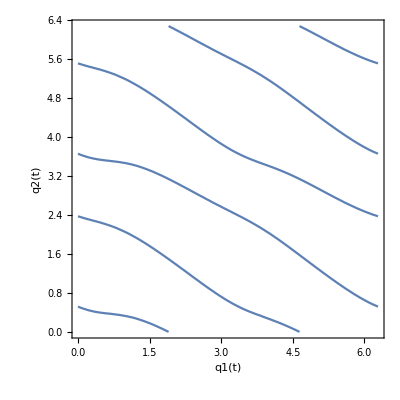

```mathematica
ContourPlot[subs2==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->Automatic]
```

```mathematica
subs3=subs2/.{q1[t]->0}//Simplify
```

{{(-0.242239+0.8303 Cos[q2[t]]^2-0.8303 Sin[q2[t]]^2-0.209776 Sin[2 q2[t]])/(-3.08822+1. Cos[2 q2[t]]-0.0705793 Sin[π/6+2 q2[t]])}}

```mathematica
sol=NSolve[subs3==0,q2[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q2[t]→-2.62332},{q2[t]→-0.765747},{q2[t]→0.518275},{q2[t]→2.37585}}

```mathematica
val=q2[t]/.sol
```

{-2.62332,-0.765747,0.518275,2.37585}

```mathematica
180 val/Pi
```

{-150.305,-43.874,29.695,136.126}

#### ==> r>2 in those cases

## u2 input

```mathematica
gx=Coefficient[xdot,u2]//Simplify ;
```

```mathematica
fx=xdot-gx u2;
```

### End effector x coordinate

```mathematica
hx=1/(2 (m0+m1+m2))(2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]);
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{((-2 l0 m0 Sin[fi0+q0[t]]-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]]) q0'[t])/(2 (m0+m1+m2))+((-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]]) q1'[t])/(2 (m0+m1+m2))-(l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]] q2'[t])/(2 (m0+m1+m2))}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify
```

{{(-2 l2 (2 m0+2 m1+m2) (8 I0 I1 m0^2+8 I0 I2 m0^2+16 I0 I1 m0 m1+16 I0 I2 m0 m1+8 I1 l0^2 m0^2 m1+8 I2 l0^2 m0^2 m1+2 I0 l1^2 m0^2 m1+8 I0 I1 m1^2+8 I0 I2 m1^2+8 I1 l0^2 m0 m1^2+8 I2 l0^2 m0 m1^2+2 I0 l1^2 m0 m1^2+l0^2 l1^2 m0^2 m1^2+16 I0 I1 m0 m2+16 I0 I2 m0 m2+8 I1 l0^2 m0^2 m2+8 I2 l0^2 m0^2 m2+8 I0 l1^2 m0^2 m2+2 I0 l2^2 m0^2 m2+16 I0 I1 m1 m2+16 I0 I2 m1 m2+16 I1 l0^2 m0 m1 m2+16 I2 l0^2 m0 m1 m2+12 I0 l1^2 m0 m1 m2+4 I0 l2^2 m0 m1 m2+6 l0^2 l1^2 m0^2 m1 m2+2 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 m1^2 m2+2 I0 l2^2 m1^2 m2+2 l0^2 l1^2 m0 m1^2 m2+2 l0^2 l2^2 m0 m1^2 m2+8 I0 I1 m2^2+8 I0 I2 m2^2+8 I1 l0^2 m0 m2^2+8 I2 l0^2 m0 m2^2+8 I0 l1^2 m0 m2^2+2 I0 l2^2 m0 m2^2+4 l0^2 l1^2 m0^2 m2^2+l0^2 l2^2 m0^2 m2^2+2 I0 l1^2 m1 m2^2+2 I0 l2^2 m1 m2^2+2 l0^2 l1^2 m0 m1 m2^2+2 l0^2 l2^2 m0 m1 m2^2-l0^2 l1^2 m0^2 (m1+2 m2)^2 Cos[2 (fi0-q1[t])]-2 l0^2 l1 l2 m0^2 m2 (m1+2 m2) Cos[2 fi0-2 q1[t]-q2[t]]-l0^2 l2^2 m0^2 m2^2 Cos[2 (fi0-q1[t]-q2[t])]+8 I0 l1 l2 m0^2 m2 Cos[q2[t]]+12 I0 l1 l2 m0 m1 m2 Cos[q2[t]]+6 l0^2 l1 l2 m0^2 m1 m2 Cos[q2[t]]+4 I0 l1 l2 m1^2 m2 Cos[q2[t]]+4 l0^2 l1 l2 m0 m1^2 m2 Cos[q2[t]]+8 I0 l1 l2 m0 m2^2 Cos[q2[t]]+4 l0^2 l1 l2 m0^2 m2^2 Cos[q2[t]]+4 I0 l1 l2 m1 m2^2 Cos[q2[t]]+4 l0^2 l1 l2 m0 m1 m2^2 Cos[q2[t]]) Sin[q0[t]+q1[t]+q2[t]]+(-(4 I0 m0+4 I1 m0+4 I2 m0+4 I0 m1+4 I1 m1+4 I2 m1+4 l0^2 m0 m1+l1^2 m0 m1+4 I0 m2+4 I1 m2+4 I2 m2+4 l0^2 m0 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+4 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]) (l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])+(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]) (4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]])) (-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]])+l0 m0 (l1 (8 I2 (m0+m1+m2) (m1+2 m2)+l2^2 m2 (2 m0 (m1+m2)+m1 (2 m1+3 m2))) Cos[fi0-q1[t]]+l2 m2 (-l1 l2 (2 m0+m1) m2 Cos[fi0-q1[t]-2 q2[t]]-(8 I1 (m0+m1+m2)-l1^2 (m1^2-4 m0 m2)) Cos[fi0-q1[t]-q2[t]]+l1^2 (2 m0+m1) (m1+2 m2) Cos[fi0-q1[t]+q2[t]])) (-2 l0 m0 Sin[fi0+q0[t]]-l1 (2 m0+m1) Sin[q0[t]+q1[t]]-l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]]))/((m0+m1+m2) (32 I0 I1 I2 m0^2+64 I0 I1 I2 m0 m1+32 I1 I2 l0^2 m0^2 m1+8 I0 I2 l1^2 m0^2 m1+32 I0 I1 I2 m1^2+32 I1 I2 l0^2 m0 m1^2+8 I0 I2 l1^2 m0 m1^2+4 I2 l0^2 l1^2 m0^2 m1^2+64 I0 I1 I2 m0 m2+32 I1 I2 l0^2 m0^2 m2+32 I0 I2 l1^2 m0^2 m2+8 I0 I1 l2^2 m0^2 m2+64 I0 I1 I2 m1 m2+64 I1 I2 l0^2 m0 m1 m2+48 I0 I2 l1^2 m0 m1 m2+16 I0 I1 l2^2 m0 m1 m2+24 I2 l0^2 l1^2 m0^2 m1 m2+8 I1 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 l2^2 m0^2 m1 m2+8 I0 I2 l1^2 m1^2 m2+8 I0 I1 l2^2 m1^2 m2+8 I2 l0^2 l1^2 m0 m1^2 m2+8 I1 l0^2 l2^2 m0 m1^2 m2+2 I0 l1^2 l2^2 m0 m1^2 m2+l0^2 l1^2 l2^2 m0^2 m1^2 m2+32 I0 I1 I2 m2^2+32 I1 I2 l0^2 m0 m2^2+32 I0 I2 l1^2 m0 m2^2+8 I0 I1 l2^2 m0 m2^2+16 I2 l0^2 l1^2 m0^2 m2^2+4 I1 l0^2 l2^2 m0^2 m2^2+4 I0 l1^2 l2^2 m0^2 m2^2+8 I0 I2 l1^2 m1 m2^2+8 I0 I1 l2^2 m1 m2^2+8 I2 l0^2 l1^2 m0 m1 m2^2+8 I1 l0^2 l2^2 m0 m1 m2^2+6 I0 l1^2 l2^2 m0 m1 m2^2+3 l0^2 l1^2 l2^2 m0^2 m1 m2^2+I0 l1^2 l2^2 m1^2 m2^2+l0^2 l1^2 l2^2 m0 m1^2 m2^2-l0^2 l1^2 m0^2 (m1+2 m2) (l2^2 m1 m2+4 I2 (m1+2 m2)) Cos[2 (fi0-q1[t])]-l0^2 l2^2 m0^2 (4 I1-l1^2 m1) m2^2 Cos[2 (fi0-q1[t]-q2[t])]-4 I0 l1^2 l2^2 m0^2 m2^2 Cos[2 q2[t]]-4 I0 l1^2 l2^2 m0 m1 m2^2 Cos[2 q2[t]]-2 l0^2 l1^2 l2^2 m0^2 m1 m2^2 Cos[2 q2[t]]-I0 l1^2 l2^2 m1^2 m2^2 Cos[2 q2[t]]-l0^2 l1^2 l2^2 m0 m1^2 m2^2 Cos[2 q2[t]]))}}

```mathematica
subs=LgLfhx/.{m0->40,m1->4,m2->3,I0->6.667,I1->0.333,I2->0.25,l0->1,l1->1,l2->1,fi0->Pi/6}//Simplify//Chop
```

{{(0.00787296 Cos[q0[t]-q1[t]]+0.0630152 Cos[q0[t]-q1[t]-q2[t]]-0.551107 Cos[q0[t]-q1[t]+q2[t]]+0.551107 Cos[q0[t]+3 q1[t]+q2[t]]+0.165332 Cos[q0[t]+3 q1[t]+2 q2[t]]+0.00454545 Sin[q0[t]-q1[t]]-0.356832 Sin[q0[t]+q1[t]]+0.0363818 Sin[q0[t]-q1[t]-q2[t]]-1.03095 Sin[q0[t]+q1[t]-q2[t]]-0.318182 Sin[q0[t]-q1[t]+q2[t]]+6.12326 Sin[q0[t]+q1[t]+q2[t]]-0.318182 Sin[q0[t]+3 q1[t]+q2[t]]+1.30777 Sin[q0[t]+q1[t]+2 q2[t]]-0.0954545 Sin[q0[t]+3 q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
ContourPlot3D[subs==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{q0,q1,q2}]
```

-Graphics3D-

```mathematica
subs2=subs/.{q0[t]->0}//Simplify
```

{{(0.00787296 Cos[q1[t]]-0.551107 Cos[q1[t]-q2[t]]+0.0630152 Cos[q1[t]+q2[t]]+0.551107 Cos[3 q1[t]+q2[t]]+0.165332 Cos[3 q1[t]+2 q2[t]]-0.361377 Sin[q1[t]]-0.712767 Sin[q1[t]-q2[t]]+6.08688 Sin[q1[t]+q2[t]]-0.318182 Sin[3 q1[t]+q2[t]]+1.30777 Sin[q1[t]+2 q2[t]]-0.0954545 Sin[3 q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
Plot3D[subs2,{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->Automatic]
```

-Graphics3D-

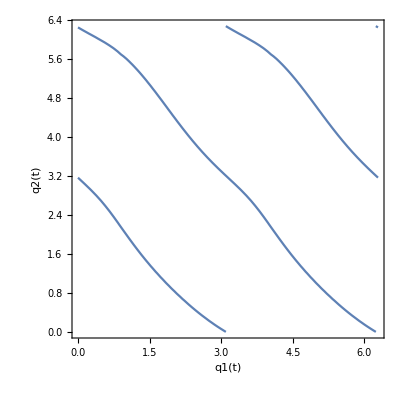

```mathematica
ContourPlot[subs2==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->Automatic]
```

```mathematica
subs3=subs2/.{q1[t]->0}//Simplify
```

{{(0.00787296+0.0630152 Cos[q2[t]]+0.165332 Cos[2 q2[t]]+6.48147 Sin[q2[t]]+1.21232 Sin[2 q2[t]])/(-4.77569+1.54642 Cos[2 q2[t]]-0.109145 Sin[π/6+2 q2[t]])}}

```mathematica
sol=NSolve[subs3==0,q2[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q2[t]→-3.11449},{q2[t]→-0.0265005}}

```mathematica
val=q2[t]/.sol
```

{-3.11449,-0.0265005}

```mathematica
180 val/Pi
```

{-178.447,-1.51837}

#### ==> r>2 in these cases

### End effector y coordinate

```mathematica
hx=(2 l0 m0 Sin[fi0+q0[t]]+l1 (2 m0+m1) Sin[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Sin[q0[t]+q1[t]+q2[t]])/(2 (m0+m1+m2));
```

#### L_gh(x) k=0

```mathematica
Lghx=D[hx,Transpose[x]].gx
```

{0}

#### L_g L_fh(x) k=1

```mathematica
Lfhx=D[hx,Transpose[x]].fx
```

{((2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]) q0'[t])/(2 (m0+m1+m2))+((l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]) q1'[t])/(2 (m0+m1+m2))+(l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]] q2'[t])/(2 (m0+m1+m2))}

```mathematica
LgLfhx=D[Lfhx,Transpose[x]].gx//Simplify
```

{{(2 l2 (2 m0+2 m1+m2) (8 I0 I1 m0^2+8 I0 I2 m0^2+16 I0 I1 m0 m1+16 I0 I2 m0 m1+8 I1 l0^2 m0^2 m1+8 I2 l0^2 m0^2 m1+2 I0 l1^2 m0^2 m1+8 I0 I1 m1^2+8 I0 I2 m1^2+8 I1 l0^2 m0 m1^2+8 I2 l0^2 m0 m1^2+2 I0 l1^2 m0 m1^2+l0^2 l1^2 m0^2 m1^2+16 I0 I1 m0 m2+16 I0 I2 m0 m2+8 I1 l0^2 m0^2 m2+8 I2 l0^2 m0^2 m2+8 I0 l1^2 m0^2 m2+2 I0 l2^2 m0^2 m2+16 I0 I1 m1 m2+16 I0 I2 m1 m2+16 I1 l0^2 m0 m1 m2+16 I2 l0^2 m0 m1 m2+12 I0 l1^2 m0 m1 m2+4 I0 l2^2 m0 m1 m2+6 l0^2 l1^2 m0^2 m1 m2+2 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 m1^2 m2+2 I0 l2^2 m1^2 m2+2 l0^2 l1^2 m0 m1^2 m2+2 l0^2 l2^2 m0 m1^2 m2+8 I0 I1 m2^2+8 I0 I2 m2^2+8 I1 l0^2 m0 m2^2+8 I2 l0^2 m0 m2^2+8 I0 l1^2 m0 m2^2+2 I0 l2^2 m0 m2^2+4 l0^2 l1^2 m0^2 m2^2+l0^2 l2^2 m0^2 m2^2+2 I0 l1^2 m1 m2^2+2 I0 l2^2 m1 m2^2+2 l0^2 l1^2 m0 m1 m2^2+2 l0^2 l2^2 m0 m1 m2^2-l0^2 l1^2 m0^2 (m1+2 m2)^2 Cos[2 (fi0-q1[t])]-2 l0^2 l1 l2 m0^2 m2 (m1+2 m2) Cos[2 fi0-2 q1[t]-q2[t]]-l0^2 l2^2 m0^2 m2^2 Cos[2 (fi0-q1[t]-q2[t])]+8 I0 l1 l2 m0^2 m2 Cos[q2[t]]+12 I0 l1 l2 m0 m1 m2 Cos[q2[t]]+6 l0^2 l1 l2 m0^2 m1 m2 Cos[q2[t]]+4 I0 l1 l2 m1^2 m2 Cos[q2[t]]+4 l0^2 l1 l2 m0 m1^2 m2 Cos[q2[t]]+8 I0 l1 l2 m0 m2^2 Cos[q2[t]]+4 l0^2 l1 l2 m0^2 m2^2 Cos[q2[t]]+4 I0 l1 l2 m1 m2^2 Cos[q2[t]]+4 l0^2 l1 l2 m0 m1 m2^2 Cos[q2[t]]) Cos[q0[t]+q1[t]+q2[t]]+(-(4 I0 m0+4 I1 m0+4 I2 m0+4 I0 m1+4 I1 m1+4 I2 m1+4 l0^2 m0 m1+l1^2 m0 m1+4 I0 m2+4 I1 m2+4 I2 m2+4 l0^2 m0 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+4 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+4 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]) (l2^2 (m0+m1) m2+4 I2 (m0+m1+m2)+l1 l2 (2 m0+m1) m2 Cos[q2[t]])+(4 I1 m0+4 I2 m0+4 I1 m1+4 I2 m1+l1^2 m0 m1+4 I1 m2+4 I2 m2+4 l1^2 m0 m2+l2^2 m0 m2+l1^2 m1 m2+l2^2 m1 m2+2 l0 l1 m0 (m1+2 m2) Cos[fi0-q1[t]]+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+4 l1 l2 m0 m2 Cos[q2[t]]+2 l1 l2 m1 m2 Cos[q2[t]]) (4 I2 m0+4 I2 m1+4 I2 m2+l2^2 m0 m2+l2^2 m1 m2+2 l0 l2 m0 m2 Cos[fi0-q1[t]-q2[t]]+l1 l2 (2 m0+m1) m2 Cos[q2[t]])) (l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]])+l0 m0 (l1 (8 I2 (m0+m1+m2) (m1+2 m2)+l2^2 m2 (2 m0 (m1+m2)+m1 (2 m1+3 m2))) Cos[fi0-q1[t]]+l2 m2 (-l1 l2 (2 m0+m1) m2 Cos[fi0-q1[t]-2 q2[t]]-(8 I1 (m0+m1+m2)-l1^2 (m1^2-4 m0 m2)) Cos[fi0-q1[t]-q2[t]]+l1^2 (2 m0+m1) (m1+2 m2) Cos[fi0-q1[t]+q2[t]])) (2 l0 m0 Cos[fi0+q0[t]]+l1 (2 m0+m1) Cos[q0[t]+q1[t]]+l2 (2 m0+2 m1+m2) Cos[q0[t]+q1[t]+q2[t]]))/((m0+m1+m2) (32 I0 I1 I2 m0^2+64 I0 I1 I2 m0 m1+32 I1 I2 l0^2 m0^2 m1+8 I0 I2 l1^2 m0^2 m1+32 I0 I1 I2 m1^2+32 I1 I2 l0^2 m0 m1^2+8 I0 I2 l1^2 m0 m1^2+4 I2 l0^2 l1^2 m0^2 m1^2+64 I0 I1 I2 m0 m2+32 I1 I2 l0^2 m0^2 m2+32 I0 I2 l1^2 m0^2 m2+8 I0 I1 l2^2 m0^2 m2+64 I0 I1 I2 m1 m2+64 I1 I2 l0^2 m0 m1 m2+48 I0 I2 l1^2 m0 m1 m2+16 I0 I1 l2^2 m0 m1 m2+24 I2 l0^2 l1^2 m0^2 m1 m2+8 I1 l0^2 l2^2 m0^2 m1 m2+2 I0 l1^2 l2^2 m0^2 m1 m2+8 I0 I2 l1^2 m1^2 m2+8 I0 I1 l2^2 m1^2 m2+8 I2 l0^2 l1^2 m0 m1^2 m2+8 I1 l0^2 l2^2 m0 m1^2 m2+2 I0 l1^2 l2^2 m0 m1^2 m2+l0^2 l1^2 l2^2 m0^2 m1^2 m2+32 I0 I1 I2 m2^2+32 I1 I2 l0^2 m0 m2^2+32 I0 I2 l1^2 m0 m2^2+8 I0 I1 l2^2 m0 m2^2+16 I2 l0^2 l1^2 m0^2 m2^2+4 I1 l0^2 l2^2 m0^2 m2^2+4 I0 l1^2 l2^2 m0^2 m2^2+8 I0 I2 l1^2 m1 m2^2+8 I0 I1 l2^2 m1 m2^2+8 I2 l0^2 l1^2 m0 m1 m2^2+8 I1 l0^2 l2^2 m0 m1 m2^2+6 I0 l1^2 l2^2 m0 m1 m2^2+3 l0^2 l1^2 l2^2 m0^2 m1 m2^2+I0 l1^2 l2^2 m1^2 m2^2+l0^2 l1^2 l2^2 m0 m1^2 m2^2-l0^2 l1^2 m0^2 (m1+2 m2) (l2^2 m1 m2+4 I2 (m1+2 m2)) Cos[2 (fi0-q1[t])]-l0^2 l2^2 m0^2 (4 I1-l1^2 m1) m2^2 Cos[2 (fi0-q1[t]-q2[t])]-4 I0 l1^2 l2^2 m0^2 m2^2 Cos[2 q2[t]]-4 I0 l1^2 l2^2 m0 m1 m2^2 Cos[2 q2[t]]-2 l0^2 l1^2 l2^2 m0^2 m1 m2^2 Cos[2 q2[t]]-I0 l1^2 l2^2 m1^2 m2^2 Cos[2 q2[t]]-l0^2 l1^2 l2^2 m0 m1^2 m2^2 Cos[2 q2[t]]))}}

```mathematica
subs=LgLfhx/.{m0->40,m1->4,m2->3,I0->6.667,I1->0.333,I2->0.25,l0->1,l1->1,l2->1,fi0->Pi/6}//Simplify//Chop
```

{{(-0.00454545 Cos[q0[t]-q1[t]]+0.356832 Cos[q0[t]+q1[t]]-0.0363818 Cos[q0[t]-q1[t]-q2[t]]+1.03095 Cos[q0[t]+q1[t]-q2[t]]+0.318182 Cos[q0[t]-q1[t]+q2[t]]-6.12326 Cos[q0[t]+q1[t]+q2[t]]+0.318182 Cos[q0[t]+3 q1[t]+q2[t]]-1.30777 Cos[q0[t]+q1[t]+2 q2[t]]+0.0954545 Cos[q0[t]+3 q1[t]+2 q2[t]]+0.00787296 Sin[q0[t]-q1[t]]+0.0630152 Sin[q0[t]-q1[t]-q2[t]]-0.551107 Sin[q0[t]-q1[t]+q2[t]]+0.551107 Sin[q0[t]+3 q1[t]+q2[t]]+0.165332 Sin[q0[t]+3 q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
ContourPlot3D[subs==0,{q0[t],0,2 Pi},{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->{q0,q1,q2}]
```

-Graphics3D-

```mathematica
subs2=subs/.{q0[t]->0}//Simplify
```

{{(0.352286 Cos[q1[t]]+1.34913 Cos[q1[t]-q2[t]]-6.15964 Cos[q1[t]+q2[t]]+0.318182 Cos[3 q1[t]+q2[t]]-1.30777 Cos[q1[t]+2 q2[t]]+0.0954545 Cos[3 q1[t]+2 q2[t]]-0.00787296 Sin[q1[t]]+0.551107 Sin[q1[t]-q2[t]]-0.0630152 Sin[q1[t]+q2[t]]+0.551107 Sin[3 q1[t]+q2[t]]+0.165332 Sin[3 q1[t]+2 q2[t]])/(-5.27569+1.54642 Cos[2 q2[t]]+1. Sin[π/6+2 q1[t]]-0.109145 Sin[π/6+2 q1[t]+2 q2[t]])}}

```mathematica
Plot3D[subs2,{q1[t],0,2 Pi},{q2[t],0,2 Pi},AxesLabel->Automatic]
```

-Graphics3D-

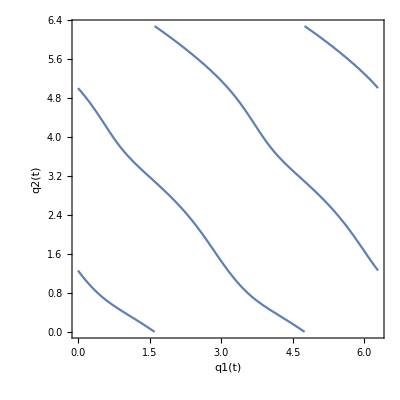

```mathematica
ContourPlot[subs2==0,{q1[t],0,2 Pi},{q2[t],0,2 Pi},FrameLabel->Automatic]
```

```mathematica
subs3=subs2/.{q1[t]->0}//Simplify
```

{{(0.352286-4.49233 Cos[q2[t]]-1.21232 Cos[2 q2[t]]-0.0630152 Sin[q2[t]]+0.165332 Sin[2 q2[t]])/(-4.77569+1.54642 Cos[2 q2[t]]-0.109145 Sin[π/6+2 q2[t]])}}

```mathematica
sol=NSolve[subs3==0,q2[t],Reals]/.C[1]->0
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{q2[t]→-1.27212},{q2[t]→1.25995}}

```mathematica
val=q2[t]/.sol
```

{-1.27212,1.25995}

```mathematica
180 val/Pi
```

{-72.8871,72.1896}

#### ==> r>2 in those cases